```mathematica
lj93[r_,ξ_,σ_]=-ξ*1.5*3^(1/2)(1/r^5)(-9 σ^9/r^6+3 σ^3)r;
lj93c[r_,ξ_,σ_]=-3/2 √3 ξ ((3 σ^3)/r^4-(9 σ^9)/r^10);
lj126[r_,ξ_,σ_]=If[r<2.5 σ,-4 ξ ((6 σ^6)/r^7-(12 σ^12)/r^13),0];
```

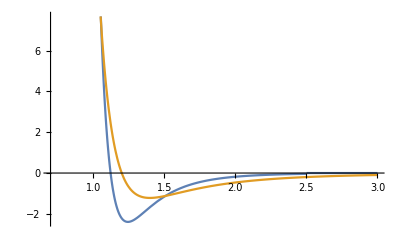

```mathematica
Plot[{lj126[r,1,1],lj93c[r,1,1]},{r,0.7,3}]
```

```mathematica
D[4ξ((σ/r)^12-(σ/r)^6),r]
```

4 ξ ((6 σ^6)/r^7-(12 σ^12)/r^13)

```mathematica
dxs=0.295;
NN=1;

funcTab={};
rands=Table[{6RandomReal[],0,6RandomReal[]},{ii,1,NN}];
For[j=1,j<=NN,j++,
forceTab={};
For[y=0.5dxs,y<=1.5dxs,y=y+0.01dxs,
totalpts=Length[grid];
(*dist = Table[{grid[[ii]]-{0,y,0}},{ii,1,totalpts}];*)
absdist=Table[((grid[[ii,1]]-rands[[j,1]])^2+(grid[[ii,2]]-y)^2+(grid[[ii,3]]-rands[[j,3]])^2)^(1/2),{ii,1,totalpts}];
force=Sum[lj126[absdist[[ii]],1,dxs](y-grid[[ii,2]])/absdist[[ii]],{ii,1,totalpts}];
AppendTo[forceTab,{y,force}];
];
(*forceFunc2=Interpolation[forceTab,InterpolationOrder->1];*)
AppendTo[funcTab,forceTab];
];
```

```mathematica
Length[funcTab]
```

20

```mathematica
func=Interpolation[funcTab[[1]],InterpolationOrder->1]
```

InterpolatingFunction[…]

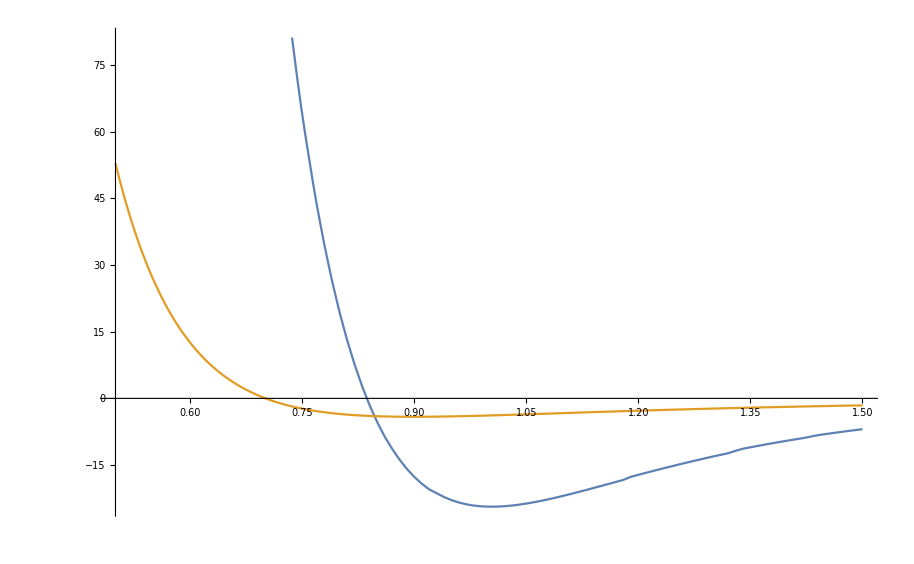

```mathematica
ljNew[r_,ξ_,σ_]= D[-4 ξ ((σ/r)^12-1.5(σ/r)^5),r];
Plot[{func[r dxs],lj93[(r+0.5) dxs,1,dxs]},{r,0.5,1.5}]
```

```mathematica
forceTab
```

{{0.01695,0.},{0.0339,0.},{0.05085,0.},{0.0678,0.},{0.08475,0.},{0.1017,0.},{0.11865,0.},{0.1356,0.},{0.15255,0.},{0.1695,0.},{0.18645,0.},{0.2034,0.},{0.22035,0.},{0.2373,0.},{0.25425,0.},{0.2712,0.},{0.28815,0.},{0.3051,0.},{0.32205,0.},{0.339,0.},{0.35595,0.},{0.3729,0.},{0.38985,0.},{0.4068,0.},{0.42375,0.},{0.4407,0.},{0.45765,0.},{0.4746,0.},{0.49155,0.},{0.5085,0.},{0.52545,0.},{0.5424,0.},{0.55935,0.},{0.5763,0.},{0.59325,0.},{0.6102,0.},{0.62715,0.},{0.6441,0.},{0.66105,0.},{0.678,0.},{0.69495,0.},{0.7119,0.},{0.72885,0.},{0.7458,0.},{0.76275,0.},{0.7797,0.},{0.79665,0.},{0.8136,0.},{0.83055,0.},{0.8475,0.}}

```mathematica
forceTab
```

```mathematica
Length[grid]
ListPointPlot3D[{grid},AspectRatio->1,AxesLabel->{"x","y","z"},BoxRatios->{1,0.1, 1}]
```

2793

-Graphics3D-

```mathematica
ptsXl=-21;
ptsXh=25;

ptsYl=-8;
ptsYh=33;

ptsZl=-8;
ptsZh=35;

dx=0.285;
rotY={{Cos[π/4],0,Sin[π/4]},{0,1,0},{-Sin[π/4],0,Cos[π/4]}};
rotX={{1,0,0},{0,Cos[0.9553166181245093],-Sin[0.9553166181245093]},{0,Sin[0.9553166181245093],Cos[0.9553166181245093]}};
grid1=Flatten[Table[{ii*dx,jj*dx,kk*dx},{ii,ptsXl,ptsXh},{jj,ptsYl,ptsYh},{kk,ptsZl,ptsZh}],2];
(*grid1={{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}};*)
grid=ParallelTable[rotX.rotY.grid1[[ii]],{ii,1,Length[grid1]}];
len=Length[grid]
For[i=1,i<=len,i++,
If[grid[[i,2]]>0.1dx,
grid =Delete[grid,i];
len--;
i--;
];
];
len=Length[grid];
For[i=1,i<=len,i++,
If[grid[[i,2]]<-2dx,
grid =Delete[grid,i];
len--;
i--;
];
];
len=Length[grid];
For[i=1,i<=len,i++,
If[grid[[i,1]]<-2 ||grid[[i,1]]>8 ||grid[[i,3]]<-2 ||grid[[i,3]]>8,
grid =Delete[grid,i];
len--;
i--;
];
];
```

86856

```mathematica
Export["~/bottomWall.dat",grid,"Table"]
```

~/bottomWall.dat

```mathematica
bottomWall = Table[{grid[[ii,1]]*10^-7,grid[[ii,2]]*10^-7-0.148*10^-7,grid[[ii,3]]*10^-7},{ii,1,Length[grid]}];
topWall = Table[{bottomWall[[ii,1]],-bottomWall[[ii,2]]+6*10^-7,bottomWall[[ii,3]]},{ii,1,Length[bottomWall]}];
ListPointPlot3D[{bottomWall,topWall},AspectRatio->1,AxesLabel->{"x","y","z"},BoxRatios->{8,9, 8}]
```

-Graphics3D-

```mathematica
bottomWall = Join[{Length[bottomWall]},bottomWall];
topWall = Join[{Length[topWall]},topWall];
Export["/home/drladiges/gigan/projects/FHDeX/exec/immersedIons/bottomWall.dat",bottomWall,"Table"];
Export["/home/drladiges/gigan/projects/FHDeX/exec/immersedIons/topWall.dat",topWall,"Table"];
```